```mathematica
Remove["Global`*"]
```

```mathematica
dV[x_, y_, z_, z0_] = 1/√(x^2+y^2+(z-z0)^2)
```

1/(√(x^2+y^2+(z-z0)^2))

```mathematica
V[x_, y_, z_] =Integrate[dV[x,y,z,z0],{z0,-1/2,1/2}]
(*Integrate is taking a very long time and
NIntegrate is evaluated to non-numerical values in the interval!*)
```

ConditionalExpression[-Log[-1+√(4 x^2+4 y^2+(1-2 z)^2)+2 z]+Log[1+2 z+√(4 x^2+4 y^2+(1+2 z)^2)],(Im[-√(-x^2-y^2)+z]≠0||Re[√(-x^2-y^2)-z]≥1/2||Re[-√(-x^2-y^2)+z]≥1/2)&&(Im[√(-x^2-y^2)+z]≠0||Re[√(-x^2-y^2)+z]≥1/2||Re[√(-x^2-y^2)+z]≤-1/2)&&(Im[√(-x^2-y^2)+z]≠0||Re[√(-x^2-y^2)+z]<-1/2||Re[√(-x^2-y^2)+z]>1/2)&&(Im[√(-x^2-y^2)-z]≠0||Im[-√(-x^2-y^2)+z]≠0||Re[√(-x^2-y^2)-z]<-1/2||Re[√(-x^2-y^2)-z]>1/2)]

```mathematica
constant = ContourPlot[V[x,y,z]/.{y->0},{x,-1,1},{z,-1,1}, PlotLegends->Automatic]
(*ContourShading->None*)
(*used along with Integrate is taking a long time!*)
```

-Graphics-

```mathematica
ContourPlot[V[x,y,z]/.{y->0},{x,-100,100},{z,-100,100}, PlotLegends->Automatic]
```

-Graphics-

```mathematica
Remove["Global`*"]
```

```mathematica
dV[x_, y_, z_, z0_] = z0/√(x^2+y^2+(z-z0)^2)
```

z0/(√(x^2+y^2+(z-z0)^2))

```mathematica
(*Don't use Integrate - takes a long time and doesn't give a solution accessible to ContourPlot. NIntegrate takes some time but it works nevertheless!*)
ContourPlot[NIntegrate[{z0/√(x^2+y^2+(z-z0)^2)}/.{y->0},{z0,-1/2,1/2}],{x,-1,1},{z,-1,1},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ContourPlot[NIntegrate[{z0/√(x^2+y^2+(z-z0)^2)}/.{y->0},{z0,-1/2,1/2}],{x,-1,1},{z,-1,1},PlotLegends->Automatic]
```

-Graphics-

```mathematica
Remove["Global`*"]
```

```mathematica
dV[x_, y_, z_, z0_,a_] = Exp[-(z0/a)^2]/√(x^2+y^2+(z-z0)^2)
```

(ⅇ^(-z0^2/a^2))/(√(x^2+y^2+(z-z0)^2))

```mathematica
Remove["Global`*"]
```

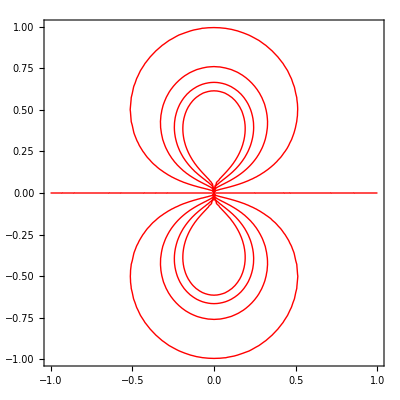

```mathematica
ContourPlot[NIntegrate[z0/Sqrt[x^2+(z-z0)^2],{z0,-0.5,0.5}],{x,-1,1},{z,-1,1},ContourShading->None,ContourStyle->Red]
```

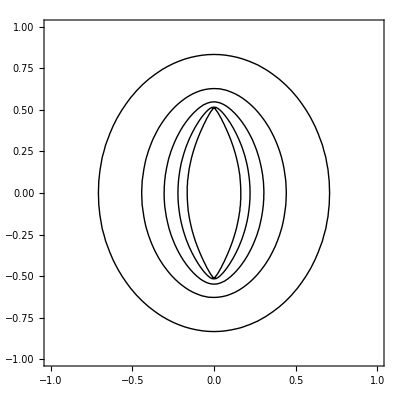

```mathematica
ContourPlot[NIntegrate[Exp[-4*z0^2]/Sqrt[x^2+(z-z0)^2],{z0,-0.5,0.5}],{x,-1,1},{z,-1,1},ContourShading->None,ContourStyle->Black]
```

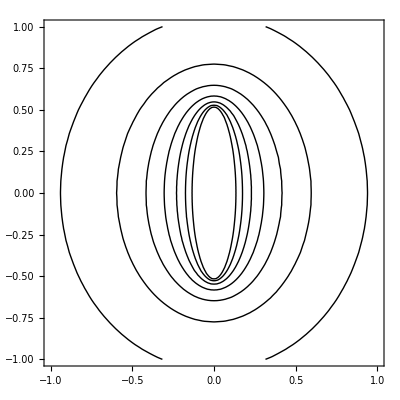

```mathematica
ContourPlot[NIntegrate[Exp[-z0^2/4]/Sqrt[x^2+(z-z0)^2],{z0,-0.5,0.5}],{x,-1,1},{z,-1,1},ContourShading->None,ContourStyle->Black]
```

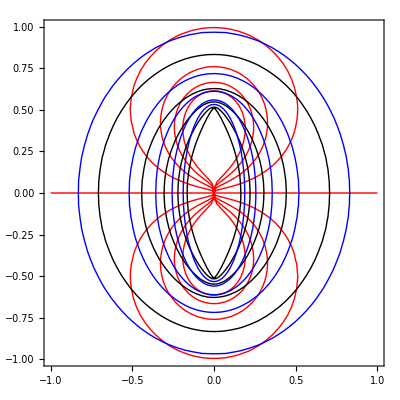

```mathematica
Show[ContourPlot[NIntegrate[z0/Sqrt[x^2+(z-z0)^2],{z0,-0.5,0.5}],{x,-1,1},{z,-1,1},ContourShading->None,ContourStyle->Red],ContourPlot[NIntegrate[Exp[-4*z0^2]/Sqrt[x^2+(z-z0)^2],{z0,-0.5,0.5}],{x,-1,1},{z,-1,1},ContourShading->None,ContourStyle->Black],ContourPlot[NIntegrate[Exp[-z0^2/4]/Sqrt[x^2+(z-z0)^2],{z0,-0.5,0.5}],{x,-1,1},{z,-1,1},ContourShading->None,ContourStyle->Blue,Contours->5]]
```

```mathematica
Remove["Global`*"]
```

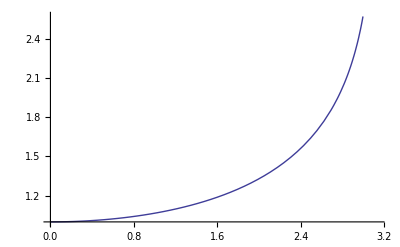

```mathematica
Plot[2^(1/2)/Pi*NIntegrate[1/(Cos[x]-Cos[a])^(1/2),{x,0,a}],{a,0.001,Pi*0.999}]
```